```mathematica
ClearAll["Global`*"];
(* Znaleźć różnicę faz φ między dwoma punktami fali dźwiękowej rozchodzącej się w powietrzu,jeżeli są one odległe od siebie o l, a częstotliwość drgań fali wynosi ν=680 Hz. Sporządzić wykres zależności
φ od l, dla l zmieniającego się od 0 m do 0,5 m. Prędkość dźwięku v=340 m/s. *)
```

```mathematica
ψ[x_]=A×Cos[k×x-ω×t];
```

```mathematica
faza1=Level[ψ[x],2][[2]]/. x-> x1
```

k x1-t ω

```mathematica
faza2=Level[ψ[x],2][[2]]/. x->x2
```

k x2-t ω

```mathematica
ϕ=faza2-faza1/. x2->l+x1//Simplify
```

k l

```mathematica
ν= 680 ;(* Hz *)
```

```mathematica
v = 340 ;(* m/s *)
```

```mathematica
λ =v/ν
```

1/2

```mathematica
k=(2× π)/λ
```

4 π

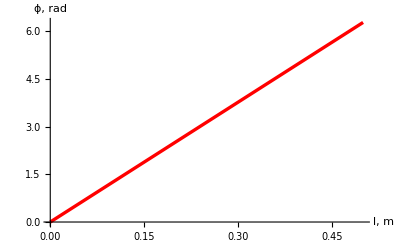

```mathematica
Plot[ϕ,{l,0,0.5},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},AxesLabel->{"l, m","ϕ, rad"}]
```